```mathematica
ClearAll["Global`*"]
```

## Метод Монте-Карло

### Нормальное распределение

1

{(ⅇ^(-1/2 (1+x)^2))/(√(2 π)),(ⅇ^(-x^2/2))/(√(2 π)),(ⅇ^(-1/2 (-1+x)^2))/(√(2 π)),(ⅇ^(-1/2 (-2+x)^2))/(√(2 π))}

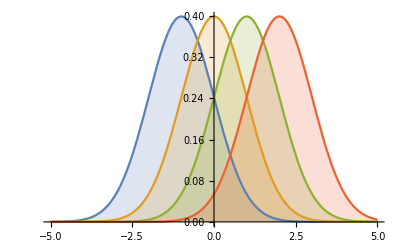

```mathematica
Clear[μ,x]
σ=1
Table[PDF[NormalDistribution[μ,σ],x],{μ,-1,2}]
Plot[%,{x,-5,5},Filling->Axis]
```

0

{ⅇ^(-2 x^2) √(2/π),(ⅇ^(-x^2/2))/(√(2 π)),1/3 ⅇ^(-(2 x^2)/9) √(2/π),(ⅇ^(-x^2/8))/(2 √(2 π))}

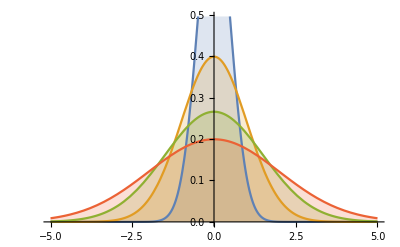

```mathematica
Clear[λ,x]
μ=0
Table[PDF[NormalDistribution[μ,σ],x],{σ,1/2,2,1/2}]
Plot[%,{x,-5,5},Filling->Axis]
```

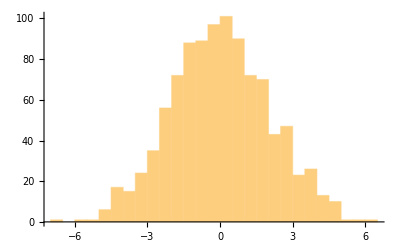

```mathematica
μ=0;
σ=2;
norm=RandomVariate[NormalDistribution[μ,σ],1000];
Histogram[norm]
```

### Усеченное распределение

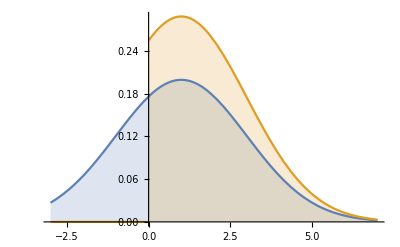

```mathematica
norm=NormalDistribution[1,2];
TD=TruncatedDistribution[{0,+∞},norm];
Plot[{PDF[norm,x],PDF[TD,x]},{x,-3,7},Filling->Axis]
```

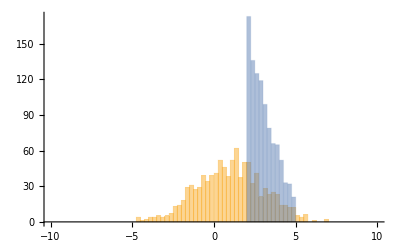

```mathematica
μ=1;
σ=2;
norm1=RandomVariate[NormalDistribution[μ,σ],1000];
norm2=RandomVariate[TruncatedDistribution[{2,5},NormalDistribution[μ,σ]],1000];
Histogram[{norm1,norm2},{-10,10,0.25}]
```

### Треугольное распределение

{Piecewise[{{x/2, 0≤x≤1}, {(4-x)/6, 1<x≤4}, {0, True}}],Piecewise[{{x/4, 0≤x≤2}, {(4-x)/4, 2<x≤4}, {0, True}}],Piecewise[{{x/6, 0≤x≤3}, {(4-x)/2, 3<x≤4}, {0, True}}]}

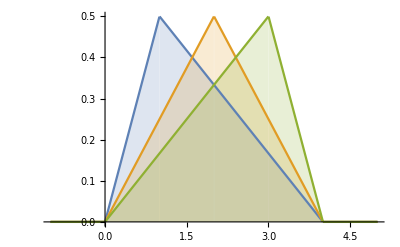

```mathematica
Clear[c,x]
Table[PDF[TriangularDistribution[{0,4},c],x],{c,1,3}]
Plot[%,{x,-1,5},Filling->Axis]
```

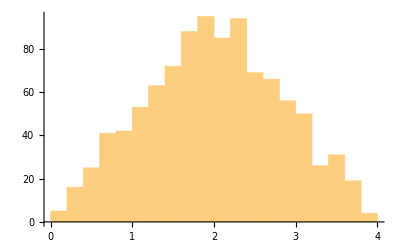

```mathematica
norm=RandomVariate[TriangularDistribution[{0,4},2],1000];
Histogram[norm]
```

### PERT распределение

{Piecewise[{{5/256 (4-x)^3 x, 0<x<4}, {0, True}}],Piecewise[{{15/512 (4-x)^2 x^2, 0<x<4}, {0, True}}],Piecewise[{{5/256 (4-x) x^3, 0<x<4}, {0, True}}]}

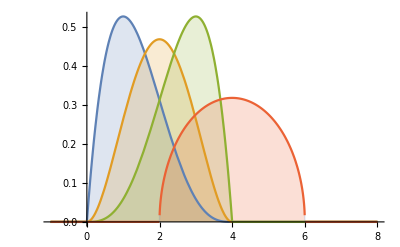

```mathematica
Clear[c,x]
Table[PDF[PERTDistribution[{0,4},c],x],{c,1,3}]
Plot[{%,PDF[PERTDistribution[{2,6},4,1],x]},{x,-1,8},Filling->Axis]
```

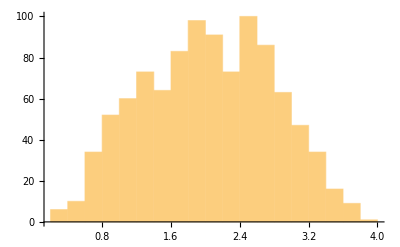

```mathematica
norm=RandomVariate[PERTDistribution[{0,4},2],1000];
Histogram[norm]
```

### Равномерное распределение

{Piecewise[{{1, 0≤x≤1}, {0, True}}],Piecewise[{{1/2, 0≤x≤2}, {0, True}}],Piecewise[{{1/3, 0≤x≤3}, {0, True}}]}

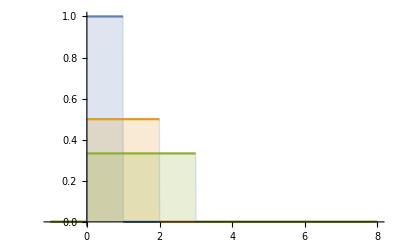

```mathematica
Clear[c,x]
Table[PDF[UniformDistribution[{0,c}],x],{c,1,3}]
Plot[%,{x,-1,8},Filling->Axis]
```

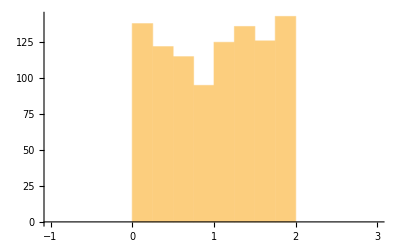

```mathematica
μ=0;
λ=2;
norm=RandomVariate[UniformDistribution[{0,2}],1000];
Histogram[norm,{-1,3,0.25}]
```

### Логонормальное распределение

{Piecewise[{{(ⅇ^(-1/2 (-1+Log[x])^2))/(√(2 π) x), x>0}, {0, True}}],Piecewise[{{(ⅇ^(-1/8 (-1+Log[x])^2))/(2 √(2 π) x), x>0}, {0, True}}],Piecewise[{{(ⅇ^(-1/18 (-1+Log[x])^2))/(3 √(2 π) x), x>0}, {0, True}}]}

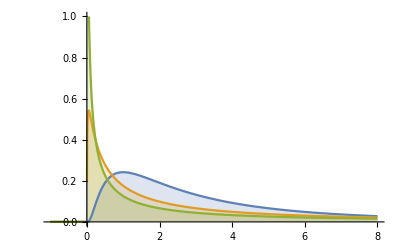

```mathematica
Clear[c,x]
μ=1;
Table[PDF[LogNormalDistribution[μ,σ],x],{σ,1,3}]
Plot[%,{x,-1,8},PlotRange->{0,1},Filling->Axis]
```

Piecewise[{{(ⅇ^(-1/2 Log[x]^2))/(√(2 π) x), x>0}, {0, True}}]

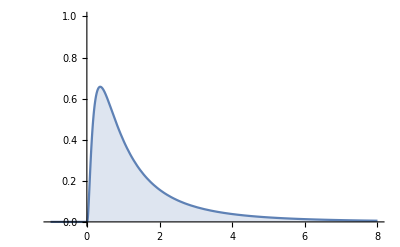

```mathematica
PDF[LogNormalDistribution[0,1],x]
Plot[%,{x,-1,8},PlotRange->{0,1},Filling->Axis]
```

Piecewise[{{(ⅇ^(-1/2 Log[x]^2))/(√(2 π) x), x>0}, {0, True}}]

Piecewise[{{(ⅇ^(-1/2 Log[-4+x]^2))/(√(2 π) (-4+x)), -4+x>0}, {0, True}}]

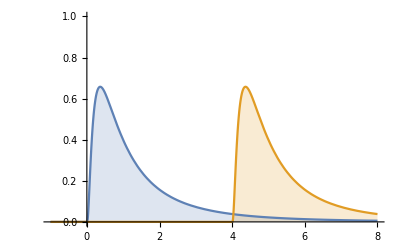

```mathematica
lognorm1=PDF[LogNormalDistribution[0,1],x]
t=4;
lognorm2= PDF[LogNormalDistribution[0,1],x-t]
Plot[{lognorm1, lognorm2},{x,-1,8},PlotRange->{0,1},Filling->Axis]
```

4

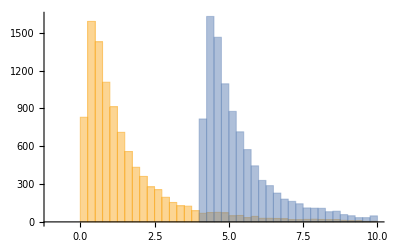

```mathematica
t=4
log1=RandomVariate[LogNormalDistribution[0,1],10000];
log2=RandomVariate[LogNormalDistribution[0,1],10000]+t;
Histogram[{log1,log2},{-1,10,0.25}]
```

## Как найти параметры закона распределения для заданного мат. ожидания и СКО

### Логонормальное распределение

```mathematica
Dist=LogNormalDistribution[1,2];
Mean[Dist]
StandardDeviation[Dist]
```

ⅇ^3

ⅇ^3 √(-1+ⅇ^4)

найдем параметры логонормального распределения для того, что бы m=1, а  s=2

```mathematica
Dist=LogNormalDistribution[a,b];
Solve[{
Mean[Dist]==1,
StandardDeviation[Dist]==2},
{a,b},Reals
]
```

{{a→-Log[5]/2,b→-√Log[5]},{a→-Log[5]/2,b→√Log[5]}}

```mathematica
Dist=LogNormalDistribution[-Log[5]/2,√Log[5]];
Mean[Dist]
StandardDeviation[Dist]
```

1

2

### Pert распределение

найдем параметры PERT  распределения для того, что бы m=1, а  s=2

```mathematica
Dist=PERTDistribution[{a,b},c]
Solve[{
Mean[Dist]==1,
StandardDeviation[Dist]==2},
{a,b,c},Reals
]
```

PERTDistribution[{a,b},c]

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→3-2 c-(2 √(56-14 c+7 c^2))/(√7),b→3-2 c+(2 √(56-14 c+7 c^2))/(√7)},{a→3-2 c+(2 √(56-14 c+7 c^2))/(√7),b→3-2 c-(2 √(56-14 c+7 c^2))/(√7)}}

```mathematica
Dist=PERTDistribution[{a,b},c]
Solve[{
c==1,
Mean[Dist]==1,
StandardDeviation[Dist]==2},
{a,b,c},Reals
]
```

PERTDistribution[{a,b},c]

{{a→1-2 √7,b→1+2 √7,c→1},{a→1+2 √7,b→1-2 √7,c→1}}

```mathematica
Dist=PERTDistribution[{1-2 √7,1+2 √7},1]
Mean[Dist]
StandardDeviation[Dist]
%//Simplify
```

PERTDistribution[{1-2 √7,1+2 √7},1]

1

1/6 √(1/7 (5+2 √7-5 (1-2 √7)) (-4+4 √7+4 (1+2 √7)))

2

## Комбинация законов распределения

### Вероятность события

```mathematica
Probability[t≤3,t\[Distributed]NormalDistribution[]]
```

1/2 (1+Erf[3/(√2)])

```mathematica
Probability[t≤3,t\[Distributed]PoissonDistribution[μ]]
```

1/6 ⅇ^-μ (6+6 μ+3 μ^2+μ^3)

```mathematica
Probability[t>2∨t<-2,t\[Distributed]NormalDistribution[]]
```

1/2 (2-Erfc[-√2]+Erfc[√2])

```mathematica
Probability[t>2∧t<-2,t\[Distributed]NormalDistribution[]]
```

0

```mathematica
Probability[x>0\[Conditioned]x>0,x\[Distributed]NormalDistribution[0,1]]
```

1

```mathematica
Probability[x>2\[Conditioned]x>0,x\[Distributed]NormalDistribution[0,1]]
```

1-Erf[√2]

```mathematica
Probability[x>2\[Conditioned]x<-2,x\[Distributed]NormalDistribution[0,1]]
```

0

```mathematica
Probability[x^2>1\[Conditioned]x>1/2,x\[Distributed]NormalDistribution[0,1]]
```

Erfc[1/(√2)]/Erfc[1/(2 √2)]

### Собственное распределение

(√2)/(π (1+x^4))

(π-ArcTan[1-√2 x]+ArcTan[1+√2 x]+ArcTanh[(√2 x)/(1+x^2)])/(2 π)

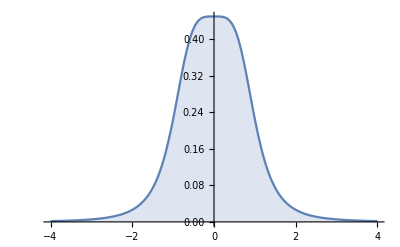

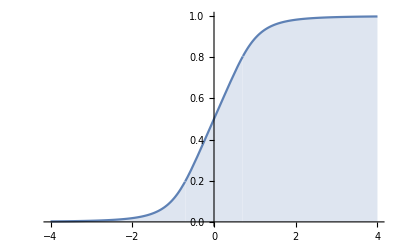

```mathematica
ClearAll["Global`*"]
prob =ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-Infinity,Infinity}];
pdfprob =PDF[prob,x]
cdfprob =CDF[prob,x]
Plot[pdfprob, {x,-4,4},Filling->Axis]
Plot[cdfprob, {x,-4,4},Filling->Axis]
```

```mathematica
Mean[prob]
Variance[prob]
```

0

1

### Преобразование вероятностных событий

```mathematica
td =TransformedDistribution[2 u+u^2,u\[Distributed]NormalDistribution[10,2]]
Mean[td]
```

TransformedDistribution[2 x+x^2,x\[Distributed]NormalDistribution[10,2]]

124

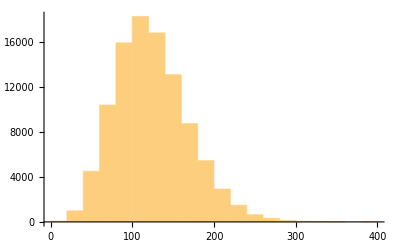

```mathematica
Histogram[RandomVariate[td,100000],{0,400,20}]
```

```mathematica
Expectation[2 u+u^2,u\[Distributed]NormalDistribution[10,2]]
```

124